```mathematica
Exit[]
```

```mathematica
g=FinancialData["DAX","1.1.2005"];
```

```mathematica
g=g[[1;;767]];
```

```mathematica
g2=Import["c:\\out.dat","Table"];
```

```mathematica
g2=Transpose[Transpose[g2][[1;;2]]];
```

```mathematica
d=Differences[Log[#2]&@@@g2];
```

```mathematica
n=Length[d];Ls=Sort[d];F=Table[{Ls[[i]],i/n},{i,1,n}];
```

```mathematica
fi=Table[{i/(n-1),Ls[[i]]},{i,n}];
```

```mathematica
Length[fi]
```

114

```mathematica
g[[1]]
```

{{2005,1,3},4291.53}

```mathematica
fi[[Length[fi]]]
```

{766/765,0.0260509}

```mathematica
f1=fi;
```

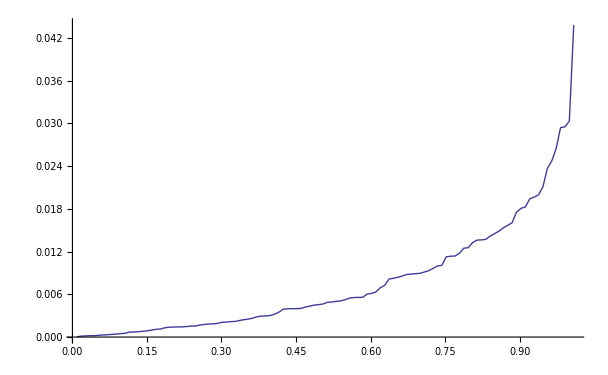

```mathematica
ListPlot[fi,PlotStyle->{PointSize[Small]},PlotRange->All,Joined->True]
```

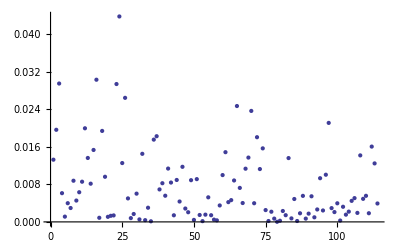

```mathematica
ListPlot[d]
```

```mathematica
fi[[1]]
```

{0,-0.016}

```mathematica
Binomial[1028,510]//N
```

6.93693×10^307

```mathematica
Po[a_,b_]:=If[b==0,1,If[b==-1,0,a^b]];
```

```mathematica
bi=Table[Binomial[Length[fi]-1,i],{i,0,Length[fi]-1}];
```

```mathematica
B[P_,t_]:=Simplify[Sum[bi[[i+1]]P[[i+1]] Po[1-t,767-i]Po[t,i],{i,0,767}]//N];
```

```mathematica
DB[P_,t_]:=Simplify[Sum[bi[[i+1]]P[[i+1]](-(767-i)Po[1-t,767-i-1]Po[t,i]+i Po[1-t,767-i]Po[t,i-1])//N,{i,0,767}]//N];
```

```mathematica
D[ Po[1-t,767-i]Po[t,i],t]
```

If[767-i==0,1,If[767-i==-1,0,(1-t)^(767-i)]] If[i==0,0,If[i==-1,0,i t^(-1+i)]]+If[767-i==0,0,If[767-i==-1,0,-(767-i) (1-t)^(766-i)]] If[i==0,1,If[i==-1,0,t^i]]

```mathematica
Bt[t0_,fi0_]:=Module[{fi=fi0,e,n,j,i,f,t=t0},
e=fi;n=Length[e];f=Table[0,{i,1,n}];
For[i=1,i≤ n,i++,
For[j=1,j≤ n-i,j++,
f[[j]]=-e[[j]]+e[[j+1]]+(1-t) f[[j]]+t f[[j+1]];
e[[j]]=e[[j]](1-t)+e[[j+1]]t;
]
];Print[#[[2]]/#[[1]]&[f[[1]]]];
e[[1]]
]
```

```mathematica
Bt[0.88,fi]
```

0.0235926

{0.88115,0.00474628}

```mathematica
#[[2]]/#[[1]]&[{1.0026143790849626,0.5973347306778085}]
```

0.595777

```mathematica
Expand[D[Bt[0.4,fi],t]]
```

{0.0117647+5.20417×10^-18 t+2.25514×10^-17 t^2-3.6169×10^-16 t^3+1.67249×10^-15 t^4-3.87624×10^-15 t^5+4.86286×10^-15 t^6-3.25434×10^-15 t^7+9.30896×10^-16 t^8,0.00863184+0.0746988 t-0.695646 t^2+2.654 t^3-5.7468 t^4+7.53966 t^5-6.01777 t^6+2.71878 t^7-0.534549 t^8}

{0.0117647+5.20417×10^-18 t+2.25514×10^-17 t^2-3.70797×10^-16 t^3+1.67943×10^-15 t^4-3.83547×10^-15 t^5+4.81082×10^-15 t^6-3.2435×10^-15 t^7+9.33498×10^-16 t^8,0.00863184+0.0746988 t-0.695646 t^2+2.654 t^3-5.7468 t^4+7.53966 t^5-6.01777 t^6+2.71878 t^7-0.534549 t^8}

```mathematica
D[-0.016+0.002877280254603279 t+0.0031124496857333626 t^2-0.0027604986750069532 t^3,t]
```

0.00287728+0.0062249 t-0.0082815 t^2

```mathematica
{0.3007843137254773,-0.0010592351269937098}
```

```mathematica
B[fi,1/500]
```

{0.00200523,-0.0142007}

```mathematica
N[fi[[2,2]],200]
```

-0.0150409

```mathematica
-0.015040906581798907
```

```mathematica
-0.015040906581798907
```

```mathematica
Length[fi]
```

768

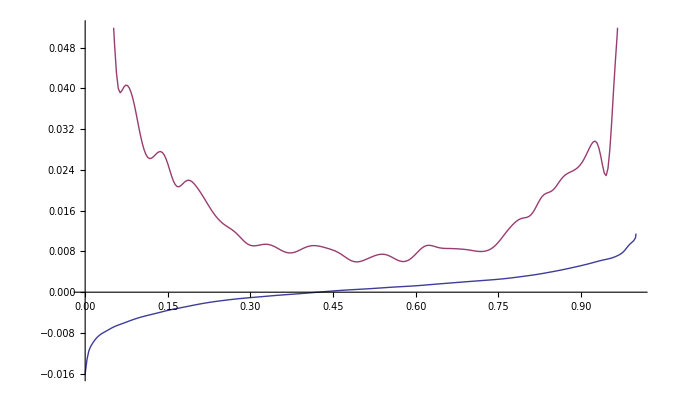

```mathematica
nN=300;tt=Table[B[fi,t/nN],{t,0,nN}];dt=Table[{tt[[t+1,1]],#[[2]]/#[[1]]&[DB[fi,t/nN]]},{t,0,nN-1}];
ListPlot[{tt,dt},Joined->True]
```

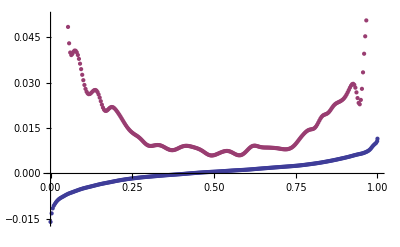

```mathematica
ListPlot[{tt,dt}]
```

```mathematica
test=Table[{i/nN//N,#[[2]]}&[dt[[i+1]]],{i,0,nN-1}];
```

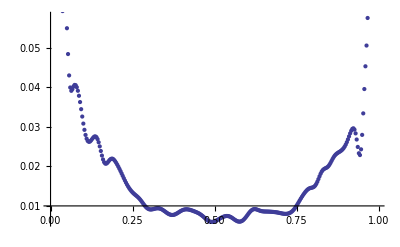

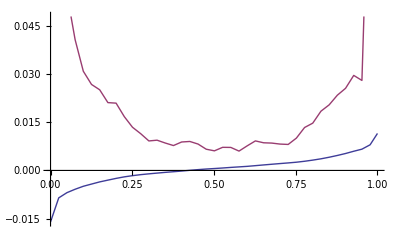

```mathematica
ListPlot[test]
```

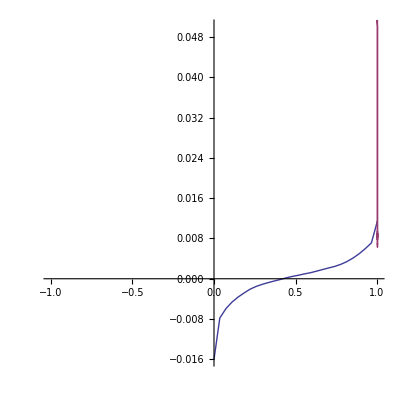

```mathematica
ParametricPlot[{B[fi,t],DB[fi,t]},{t,0,1},AspectRatio->1,PlotPoints->28,MaxRecursion->0]
```

```mathematica
nN=50;tt=Table[B[fi,i/nN],{i,0,nN}];
```

```mathematica
dd=Table[{tt[[i+1,1]],(#[[2]]/#[[1]])&[D[B[fi,t],t]/.t->i/nN]},{i,0,nN}]//N;
```

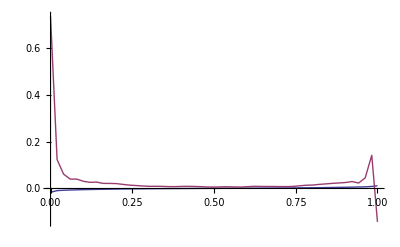

```mathematica
ListPlot[{tt,dd},Joined->True,PlotRange->All]
```

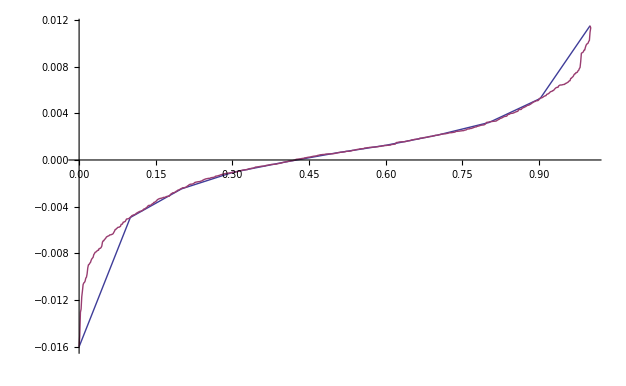

```mathematica
ListPlot[{tt,fi},Joined->True,PlotRange->All]
```

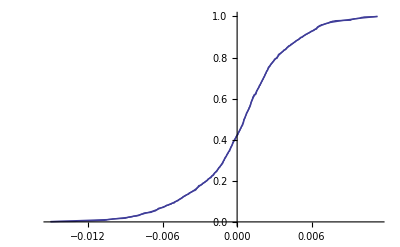

```mathematica
Show[ListPlot[B[F,#]&/@tt,Joined->True],ListPlot[F,Joined->True,PlotStyle->{PointSize[Small]}]]
```

```mathematica
%
```

```mathematica
f=Normal[Series[-Cos[3x],{x,0.5,10}]]
```

-0.0707372+2.99248 (-0.5+x)+0.318317 (-0.5+x)^2-4.48873 (-0.5+x)^3-0.238738 (-0.5+x)^4+2.01993 (-0.5+x)^5+0.0716214 (-0.5+x)^6-0.432842 (-0.5+x)^7-0.0115106 (-0.5+x)^8+0.0541052 (-0.5+x)^9+0.00115106 (-0.5+x)^10

Inverse::nonopt: Options expected (instead of y) beyond position 1 in Inverse[-Cos[3\ y], y]. An option must be a rule or a list of rules.

Inverse::nonopt: Options expected (instead of 0.0000204286) beyond position 1 in Inverse[-1., 0.0000204286]. An option must be a rule or a list of rules.

Inverse::nonopt: Options expected (instead of 0.0204286) beyond position 1 in Inverse[-0.998123, 0.0204286]. An option must be a rule or a list of rules.

General::stop: Further output of Inverse :: "nonopt" will be suppressed during this calculation.

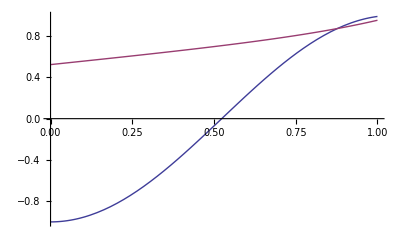

```mathematica
Plot[{f,g,Inverse[-Cos[3y],y]/.y->x},{x,0,1}]
```

```mathematica
g=Normal[InverseSeries[Series[-Cos[3x],{x,0.5,10}]]]
```

0.5+0.33417 (0.0707372+x)-0.0118786 (0.0707372+x)^2+0.0568196 (0.0707372+x)^3-0.00902878 (0.0707372+x)^4+0.0265961 (0.0707372+x)^5-0.00767575 (0.0707372+x)^6+0.0167681 (0.0707372+x)^7-0.00689638 (0.0707372+x)^8+0.0122862 (0.0707372+x)^9-0.00641364 (0.0707372+x)^10

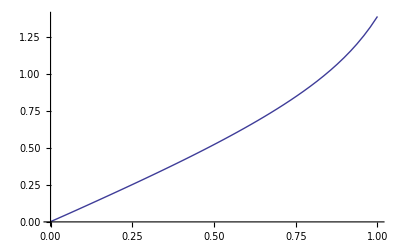

```mathematica
Plot[g,{x,0,1}]
```

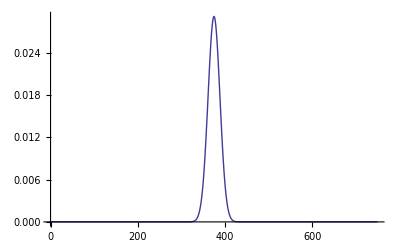

```mathematica
Plot[PDF[NormalDistribution[p nN,Sqrt[nN p (1-p)]],x],{x,0,750},PlotRange->All]
```

```mathematica
p=0.001;nN=750;m=50;Plot[n!,{n,0,1000},PlotRange->All]
```

```mathematica
Binomial[1000,400]
```

496527238625422886115073562889623132621341353659827604662932184012645905732096457382164964136575507417172339042089778751904887857092411910579077412408539948204974129778390437393954251676800524680653478266662364352619244180931154020701111982328000776980305955525649501369943202079996789539150

```mathematica
g[[1]]
```

{{1990,11,26},1443.2}

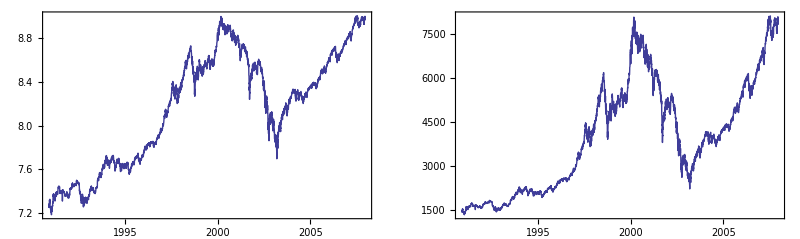

```mathematica
GraphicsRow[{DateListPlot[{{#1,Log[#2]}&@@@g},Joined->True],DateListPlot[{g},Joined->True]}]
```

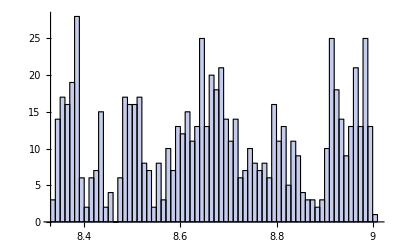

```mathematica
Histogram[Log[#2]&@@@g,HistogramCategories->50]
```

```mathematica
d=Differences[Log[10,#2]&@@@g];
```

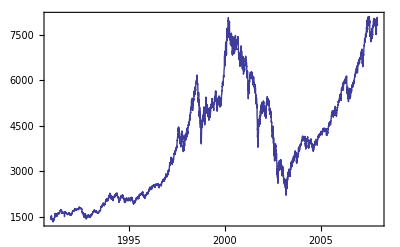

```mathematica
DateListPlot[{g},Joined->True]
```

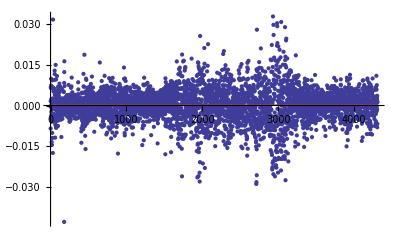

```mathematica
Show[ListPlot[d,PlotRange->All],Plot[{,Mean[d]},{x,0,Length[d]}]]
```

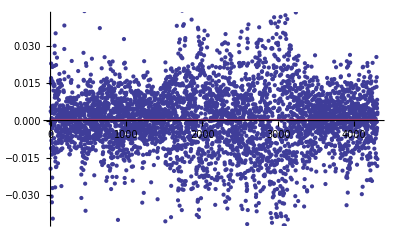

```mathematica
Show[ListPlot[10^d-1],Plot[{,10^Mean[d]-1},{x,0,Length[d]}]]
```

```mathematica
Mean[d]
Log[10,g[[Length[g],2]]/g[[1,2]]]/Length[d]
```

0.000357102

0.000357102

```mathematica
U={g[[1,2]]};
For[i=0,i<Length[d],i++,
AppendTo[U,U[[i+1]] 10^(d[[i+1]]) ];
]
```

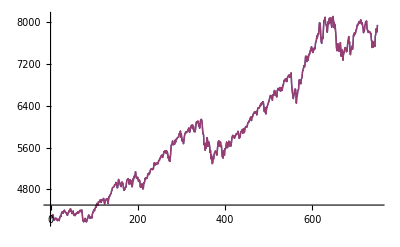

```mathematica
ListPlot[{U,#2&@@@g},Joined->True]
```

```mathematica
<<Histograms`
```

HistogramCategories::shdw: Symbol "HistogramCategories" appears in multiple contexts {"Histograms`", "Global`"}; definitions in context "Histograms`" may shadow or be shadowed by other definitions.

Histogram::shdw: Symbol "Histogram" appears in multiple contexts {"Histograms`", "Global`"}; definitions in context "Histograms`" may shadow or be shadowed by other definitions.

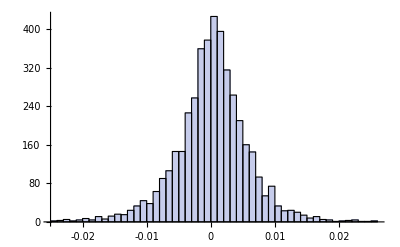

```mathematica
Histogram[d,HistogramCategories->80;HistogramRange->{-.025,.025}]
```

```mathematica
sd[i_,n_]:=If[i==1,0,StandardDeviation[d[[Max[i-n+1,1];;i]]]]
```

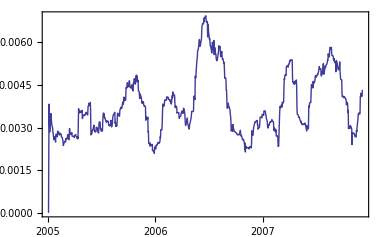

```mathematica
DateListPlot[Table[{g[[i,1]],sd[i,30] },{i,1,Length[d]}],Joined->True]
```

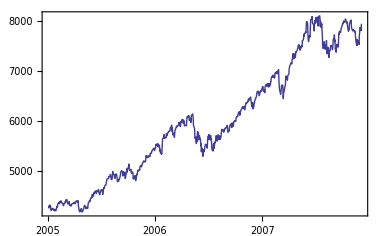

```mathematica
DateListPlot[{g},Joined->True]
```

```mathematica
vd=FinancialData["V1X","1.1.2005"];
```

FinancialData::notent: "V1X" is not a known entity in FinancialData.

```mathematica
g
```

{{{2005,2,24},0.22},{{2005,6,23},0.22},{{2005,9,22},0.22},{{2005,12,22},0.25},{{2006,2,23},0.25},{{2006,6,22},0.25},{{2006,9,21},0.25},{{2006,12,21},0.28},{{2007,2,22},0.28},{{2007,6,21},0.28},{{2007,9,20},0.28}}